# SARIMAX (до 31.03.2020)

I 
I.I Для ряда пассажирских авиаперевозок постройте прогнозную модель вида (3).
-Graphics-
Подумайте, как можно модифицировать модель на случай мультипликативной
сезонности. 

I.II Постройте вашу собственную модель, учитывающую мультипликативную
сезонность. Отобразите результат на графике.

II. Найдите остатки построенной модели. Является ли ряд остатков стационарным? Для
проверки отобразите ряд остатков и воспользуйтесь критерием Дики-Фуллера
(UnitRootTest в математике).

III. Постройте авторегрессионную модель прогнозирования ряда остатков. Итоговую
модель SARIMAX отобразите на графике

## I

```mathematica
passengers  = ExampleData[{ "Statistics","InternationalAirlinePassengers"},"TimeSeries"];
passengers
```

TimeSeries[…]

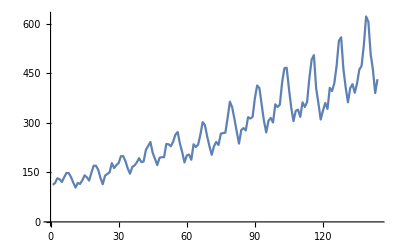

```mathematica
data = Normal[passengers];
pass = data[[All,2]];
ListLinePlot[pass]
```

## I.I Аддитивная сезонность

## Функции

```mathematica
ϕ[i_,s_,t_]:=Sin[(2π*(i-1))/s]
γ[i_,s_,t_]:=Cos[(2π*(i-1))/s]
aw[t_,s_,m_]:=Sum[Subscript[θ, j]*t^j,{j,0,m}]+Subscript[β, 1]*ϕ[Mod[t,s],s,t]+Subscript[β, 2]*γ[Mod[t,s],s,t]
params[i_]:=Subscript[θ, i]
e[t_,s_,m_]:=Sum[Subscript[θ, j]*t^j,{j,0,m}]
aORmS[m_,s_,pass_,type_]:=Module[{ts=Range[1,Length@pass]},new = e[ts,s,m];
full=Minimize[Total@((new-pass)^2),Thread[params[Range[0,m]]]]//N;
f = new/.full[[2]];
new = type[ts,s,m]/.full⟦2⟧;
full = Minimize[Total@((new-pass)^2),{Subscript[β, 1],Subscript[β, 2]}];
f = new/.full[[2]]]
```

## Параметры

```mathematica
m=2;
s=12;
ts=Range[1,Length@pass];
```

## Результат

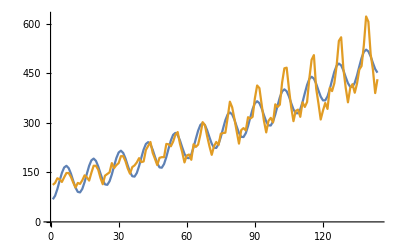

```mathematica
ListLinePlot[{passAM=aORmS[m,s,pass,aw],pass}]
```

## MSE

```mathematica
(Total@((passAM-pass)^2))/(Length@pass)
```

920.273

## I.II Мультипликативная сезонность

С ростом ряда необходимо увеличение амплитуды колебаний, поэтому я домножил на t.

## Добавление мультипликативности

```mathematica
am[t_,s_,m_]:=Sum[Subscript[θ, j]*t^j,{j,0,m}]+Subscript[β, 1]*ϕ[Mod[t,s],s,t]*t+Subscript[β, 2]*γ[Mod[t,s],s,t]*t
```

## Результат

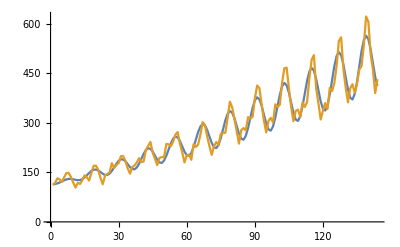

```mathematica
ListLinePlot[{passSM=aORmS[m,s,pass,am],pass}]
```

## MSE

```mathematica
(Total@((passSM-pass)^2))/(Length@pass)
```

586.584

Будем использовать данную модель для дальнейших расчетов из-за лучшего показателя MSE-метрики.

## II

```mathematica
residuals = pass - passSM;
UnitRootTest[residuals,Automatic,{"DickeyFullerF","DickeyFullerT"}]
```

{4.74565×10^-9,1.28771×10^-9}

Тест Dickey-Fuller показывает, что ряд с большой вероятностью является стационарным. Но данный тест не является до конца точным. Посмотрим на график.

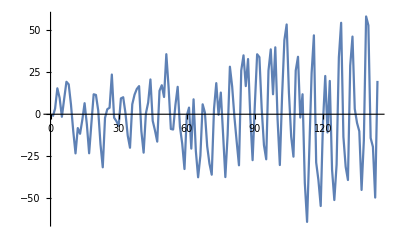

```mathematica
ListLinePlot[residuals]
```

У преобразованного ряда не до конца стабилизирована дисперсия, поэтому ряд не является стационарным. Это можно исправить путем сезонного дифференцирования.

## III

Построим модель SARIMA.

```mathematica
tsm=TimeSeriesModelFit[residuals,{"SARIMA"}];
sarimaxPRED = passSM+Table[tsm[i], {i, 1, Length[pass]}];
```

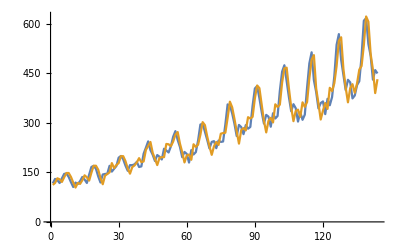

```mathematica
ListLinePlot[{sarimaxPRED,pass}]
```

## MSE

```mathematica
(Total@((sarimaxPRED-pass)^2))/(Length@pass)
```

752.954

Построена SARIMAX модель. Задание выполнено.